# Boosted Dark Matter Fluxes

## Interactions of Cosmic Rays with intergalactic and atmospheric baryons to produce boosted dark matter

## Reproducing the Pospelov Results

### Calculations

We define the maximum and minimum energy functions that arise from the kinematics,

```mathematica
Tmax[Ti_, mi_, mchi_] =  (Ti^2+2mi Ti)/(Ti+(mi+mchi)^2/(2mchi));
Tmin[Tchi_, mi_, mchi_] = (Tchi/2-mi)(1+(1 + (2Tchi)/mchi (mi + mchi)^2/(2mi - Tchi)^2)^(1/2))HeavisideTheta[Tchi - 2mi] +(Tchi/2-mi)(1-(1 + (2Tchi)/mchi (mi + mchi)^2/(2mi - Tchi)^2)^(1/2))HeavisideTheta[2mi - Tchi] ;
```

Next we parametrise the cosmic ray flux for both the protons and the Helium components using the values in the table. For protons this is;

```mathematica
ap0 = 94.1;
ap1 = -831; 
ap2 = 0; 
ap3 = 16700; 
ap4 = -10200; 
ap5=0; 
bp = 10800; 
cp =8590; 
dp1 = -4230000; 
dp2 = 3190; 
ep1 = 274000; 
ep2 = 17.4; 
fp1 = -39400; 
fp2 = 0.464; 
gp = 0;
GV = 1;
```

```mathematica
Fp[R_] = R^-2.7 (HeavisideTheta[R - 1 GV](bp + cp/R + dp1/(dp2 + R) + ep1/(ep2 + R) + fp1/(fp2 + R) + gp R)+HeavisideTheta[1 GV- R](ap0 + ap1 R + ap2 R^2 + ap3 R^3 + ap4 R^4 + ap5 R^5));
```

And also for the Helium component,

```mathematica
ah0 = 1.14;
ah1 = 0; 
ah2 = -118; 
ah3 = 578; 
ah4 = 0; 
ah5=-87; 
bh = 3120; 
ch =-5530; 
dh1 = 3370; 
dh2 = 1.29; 
eh1 = 134000; 
eh2 = 88.5; 
fh1 = -1170000; 
fh2 = 861; 
gh = 0.03;
GV = 1;
```

```mathematica
Fh[R_] = R^-2.7 (HeavisideTheta[R - 1 GV](bh + ch/R + dh1/(dh2 + R) + eh1/(eh2 + R) + fh1/(fh2 + R) + gh R)+HeavisideTheta[1 GV- R](ah0 + ah1 R + ah2 R^2 + ah3 R^3 + ah4 R^4 + ah5 R^5));
```

The rigidity can then be defined in terms of the energy;

```mathematica
R[A_,Z_,T_,T0_] = A/Z(T^2 + 2 T T0)^(1/2);
```

Where T_0 is the proton or helium rest mass. In units of GeV/c^2 these are given by;

```mathematica
mp = 0.9383;
mh = 4.03188 mp;
```

With the rigidity definition above, we can compute the differential cosmic ray flux dϕ_i/dT_i for both the proton component and Helium,

```mathematica
Rp[T_] = R[1, 1, T, mp];
dRp[T_] = D[Rp[T], T];
Rh[T_] = R[4, 2, T, mh];
dRh[T_] = D[Rh[T], T];
dPpdTi[Ti_] = 4 Pi Fp[Rp[Ti]] dRp[Ti];
dPhdTi[Ti_] = 4 Pi Fh[Rh[Ti]] dRh[Ti];
```

To obtain the final expression, we need to compute the form factors, note that the Λ_i are quoted in GeV.

```mathematica
Λp = 0.770;
Λh = 0.410;
Gp[x_] = (1+x/Λp^2)^-2;
Gh[x_] = (1+x/Λh^2)^-2;
```

For given choices of D_eff, ρ_loc, m_χ and σ_χ, we can now compute dϕ_χ/dT_χ as;

```mathematica
dPchidTchi[Tchi_, Deff_, ρ_, mchi_, σ_] := (Deff ρ σ)/mchi(Gp[2 mchi Tchi]^2 NIntegrate[dPpdTi[Ti]/Tmax[Ti, mp, mchi], {Ti, Tmin[Tchi, mp, mchi], 10^10}] + Gh[2 mchi Tchi]^2 NIntegrate[dPhdTi[Ti]/Tmax[Ti, mh, mchi], {Ti, Tmin[Tchi, mh, mchi], 10^10}]);
```

We can now try and generate the plot as shown in Fig. 1. We choose some relevant values;

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ti near {Ti} = {0.0000301982}. NIntegrate obtained 3.15012×10^11 and 3.33425×10^9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ti near {Ti} = {0.0000353078}. NIntegrate obtained 2.45936×10^8 and 1.03055×10^6 for the integral and error estimates.

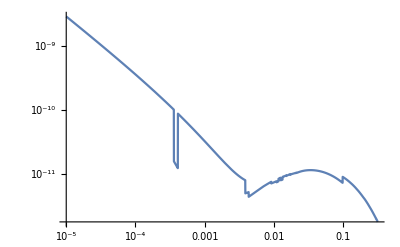

```mathematica
Deff=0.997 3.086 10^21;
σ =10^-30;
mchi1 = 0.001;
mchi2=0.01;
mchi3 =0.1;
mchi4=1;
mchi5=10;
ρ=0.3 10^-6 ;
LogLogPlot[Tchi dPchidTchi[Tchi, Deff, ρ, mchi4, σ], {Tchi, 10^-5, 10^-0.5}]
```